### Worldline instantons in an “inflation” metric: the β = 0 starting point

Independent reproduction of Sec. III A–B of P. Semrén and G. Torgrimsson, “Worldline instantons for nonperturbative particle production by space and time dependent gravitational fields”, arXiv:2508.01901.

The pair-production probability is P ~ exp(−𝒜). Its exponent follows from a saddle point of the worldline path integral: a geodesic in complex proper time u, called a worldline instanton. The complex middle part of the instanton describes the formation (tunnelling) region; its two ends become the real trajectories of the produced particle and antiparticle.

Metric (Eq. 21):  ds.b2 = dt.b2 − e^{2A(t,x)} dx.b2,  with  A = α tanh(ωt) sech.b2(kx)  (Eq. 24).
Here β = k/ω = 0, so the metric depends on t only. In units ω = 1:  A(t) = α tanh t.

α = 1 and p = 0.57 (close to the saddle-point momentum p_s) reproduce Fig. 2 of the paper.
The complex u-plane is covered by −2 < Re u < 2 and −4 < Im u < 4.
Exact rational inputs are used so that NDSolve can work at the requested precision.

The instanton starts at the branch point t_B (Eq. 27). For β = 0, Eq. (22) integrates once to (Eq. 25)
   ẋ = p e^{−2A(t)},   ṫ = √(1 + p.b2 e^{−2A(t)}).
The middle of the instanton is the turning point ṫ = 0, i.e. e^{2A(t_B)} = −p.b2, which gives
   t_B = arctanh[(iπ + ln p.b2)/(2α)].

```mathematica
ClearAll["Global`*"];

tInterp=Import[saveDir<>"tInterp.wdx"];

alpha=SetPrecision[1,50];
p=SetPrecision[57/100,50];

Rmin=-4;
Rmax=4;

urMin=-2;
urMax=2;

xdot[R_?NumericQ,ur_?NumericQ]:=p* Exp[-2 *alpha *Tanh[tInterp[R,ur]]];
```

Geodesic equations (Eq. 22), with dots denoting d/du:
   ẗ = (1 − ṫ.b2) ∂_t A,     ẍ = −2 ṫ ẋ ∂_t A − ẋ.b2 ∂_x A.
The first form follows from Γ^t_xx = .bd ∂_t e^{2A} and the on-shell condition ṫ.b2 − e^{2A} ẋ.b2 = 1 (Eq. 8).
For β = 0, ∂_x A = 0.

Initial conditions at u = 0:  t = t_B,  ṫ = 0,  x = 0,  ẋ = p e^{−2A(t_B)}.

The solution is first obtained along the imaginary axis u = iR (the “backbone”).
Since d/du = −i d/dR, with T(R) = t(iR) and X(R) = x(iR):
   T’’ = −(1 + T’.b2) ∂_t A(T),     X’’ = −2 T’ X’ ∂_t A(T),     X’(0) = i ẋ(0).

### solving eqn 22

```mathematica
A[t_]:=alpha*Tanh[t];
At[t_]:=alpha*Sech[t]^2;

tB=ArcTanh[(I*Pi+Log[p^2])/(2*alpha)];


Rstep=0.02;
urStep=0.01;

RGrid=Range[Rmin,Rmax,Rstep];
urGrid=Range[urMin,urMax,urStep];
```

```mathematica
solBackbone=NDSolve[{T''[R]==-(1+T'[R]^2) At[T[R]],X''[R]==-2 T'[R] X'[R] At[T[R]],T[0]==tB,T'[0]==0,X[0]==0,X'[0]==I*p*Exp[-2*A[tB]]},{T,X},{R,Rmin,Rmax},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->30,MaxSteps->Infinity];

Tfun[R_?NumericQ]:=Evaluate[T[R]/. solBackbone[[1]]];

Xfun[R_?NumericQ]:=Evaluate[X[R]/. solBackbone[[1]]];

dTfun[R_?NumericQ]:=Evaluate[T'[R]/. solBackbone[[1]]];

dXfun[R_?NumericQ]:=Evaluate[X'[R]/. solBackbone[[1]]];
```

NDSolve::precw: The precision of the differential equation ({{T''[R]==1. Sech[T[R]]^2 (-1-((«1»)^(«1»)[«1»])^2),X''[R]==-2. Sech[T[R]]^2 T'[R] X'[R],T[0]==-0.153196323224811534285691870146092805293132394429+1.043551136431598870876835144216887958609273346129 ⅈ,T'[0]==0,X[0]==0,X'[0]==0.-1.75438596491228070175438596491228070175438596491 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

```mathematica
horizontalData=Table[Module[{t0,dt0,x0,dx0,sol},t0=Tfun[R0];
dt0=-I*dTfun[R0];
x0=Xfun[R0];
dx0=-I*dXfun[R0];
sol=NDSolve[{t''[ur]==(1-t'[ur]^2) At[t[ur]],x''[ur]==-2 t'[ur] x'[ur] At[t[ur]],t[0]==t0,t'[0]==dt0,x[0]==x0,x'[0]==dx0},{t,x},{ur,urMin,urMax},WorkingPrecision->40,AccuracyGoal->20,PrecisionGoal->20,MaxSteps->Infinity];
Table[{ur,R0,Evaluate[t[ur]/. sol[[1]]],Evaluate[x[ur]/. sol[[1]]],Evaluate[t'[ur]/. sol[[1]]],Evaluate[x'[ur]/. sol[[1]]]},{ur,urGrid}]],{R0,RGrid}];

flatData=Flatten[horizontalData,1];

tGrid=Partition[flatData[[All,3]],Length[urGrid]];
tdotGrid = Partition[flatData[[All,5]],Length[urGrid]]
xGrid2=Partition[flatData[[All,4]],Length[urGrid]];
xdotGrid = Partition[flatData[[All,6]],Length[urGrid]]
tInterp2=ListInterpolation[tGrid,{{Rmin,Rmax},{urMin,urMax}},InterpolationOrder->1];
tdotInterp2=ListInterpolation[tdotGrid,{{Rmin,Rmax},{urMin,urMax}},InterpolationOrder->1];
xInterp2=ListInterpolation[xGrid2,{{Rmin,Rmax},{urMin,urMax}},InterpolationOrder->1];
xdotInterp2=ListInterpolation[xdotGrid,{{Rmin,Rmax},{urMin,urMax}},InterpolationOrder->1];
```

```mathematica
Rc=1.06595;

greenContour=Graphics[{Directive[Green,Thick],(*upper horizontal*)Line[{{-2,Rc},{-Rc,Rc}}],(*diagonal*)Line[{{-Rc,Rc},{Rc,-Rc}}],(*lower horizontal*)Line[{{Rc,-Rc},{2,-Rc}}]}];

x=Show[ComplexPlot[xInterp2[Im[u],Re[u]],{u,urMin+I*Rmin,urMax+I*Rmax},ColorFunction->"CyclicReImLogAbs",PlotPoints->120,MaxRecursion->3,ImageSize->Large,FrameLabel->{"Re[u]","Im[u]"},PlotLabel->"x(u) from Eq. 22"], greenContour]
```

-Graphics-

```mathematica
t=Show[ComplexPlot[tInterp2[Im[u],Re[u]],{u,urMin+I*Rmin,urMax+I*Rmax},ColorFunction->"CyclicReImLogAbs",PlotPoints->120,MaxRecursion->3,ImageSize->Large,FrameLabel->{"Re[u]","Im[u]"},PlotLabel->"t(u) from Eq. 22"],greenContour]
```

-Graphics-

```mathematica
tprime=Show[ComplexPlot[tdotInterp2[Im[u],Re[u]],{u,urMin+I*Rmin,urMax+I*Rmax},ColorFunction->"CyclicReImLogAbs",PlotPoints->120,MaxRecursion->3,ImageSize->Large,FrameLabel->{"Re[u]","Im[u]"},PlotLabel->"t'(u) from Eq. 22"],greenContour]
```

-Graphics-

```mathematica
xprime=Show[ComplexPlot[xdotInterp2[Im[u],Re[u]],{u,urMin+I*Rmin,urMax+I*Rmax},ColorFunction->"CyclicReImLogAbs",PlotPoints->120,MaxRecursion->3,ImageSize->Large,FrameLabel->{"Re[u]","Im[u]"},PlotLabel->"x'(u) from Eq. 22"],greenContour]
```

-Graphics-

The instanton must become real at both ends, so that it describes real asymptotic particles. At the saddle-point momenta this requires (Eq. 20)
   Im t = Im x = Im ṫ = Im ẋ = 0.

On the imaginary axis, t(u) becomes real at u = iRc. Since Eq. (22) has real coefficients, t, x, ṫ, ẋ then stay real along the whole horizontal line Im u = Rc, including the corner u = −Rc + iRc.

Contour (green line): horizontal for Re u < −Rc, diagonal from −Rc + iRc to Rc − iRc, then horizontal again. Beyond the corners the solution stays real, so the integration can stop there.

Checks:
  (i) integrating straight along the diagonal to the corner gives vanishing imaginary parts (Eq. 20);
  (ii) the diagonal route and the grid route give the same values at the corner, so no singularity lies between them and the contour is unambiguous.
Small residuals (~10⁻⁴) come from p = 0.57 being only approximately p_s, and from the linear interpolation.

### green contour selection

```mathematica
cp=ComplexPlot[tInterp2[Im[u],Re[u]],{u,urMin+I*Rmin,urMax+I*Rmax},ColorFunction->"CyclicReImLogAbs",PlotPoints->120,MaxRecursion->3,Frame->False];

contours=Show[ContourPlot[Im[tInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Red,Thick},Frame->False],ContourPlot[Im[xInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Blue,Thick},Frame->False],ContourPlot[Im[tdotInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Green,Thick},Frame->False],ContourPlot[Im[xdotInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Purple,Thick},Frame->False]];

Show[cp,contours,PlotRange->All]
```

-Graphics-

{1.06,1.07}

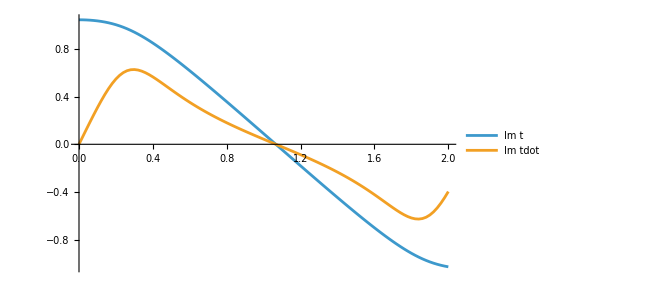

```mathematica
upperData=Table[{R,Im[tInterp2[R,0]],Im[tdotInterp2[R,0]]},{R,0,2,0.01}];
Select[upperData,Abs[#[[2]]]<10^-2&&Abs[#[[3]]]<10^-2&][[All,1]]
```

```mathematica
upperBranch=Table[{ur,Im[tInterp2[1.07,ur]],Im[tdotInterp2[1.07,ur]]},{ur,-2,0,0.001}];
zeros=Select[upperBranch,Abs[#[[2]]]<10^-2&&Abs[#[[3]]]<10^-2&];
zeros[[All,1]]
```

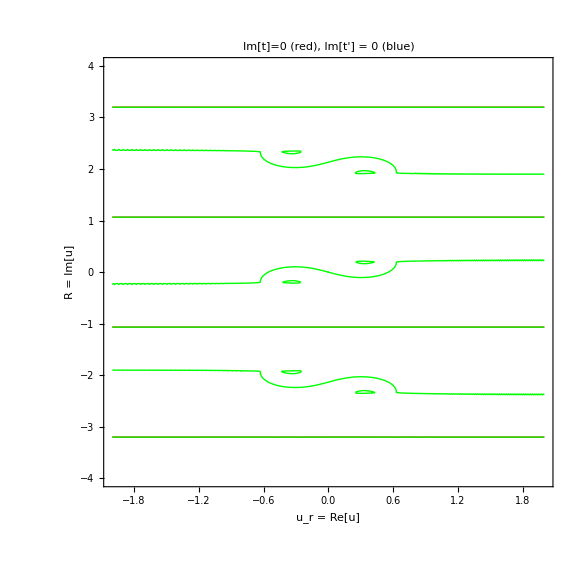

```mathematica
Show[ContourPlot[Im[tInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Red,Thick},PlotPoints->100,MaxRecursion->2],ContourPlot[Im[tdotInterp2[R,ur]],{ur,urMin,urMax},{R,Rmin,Rmax},Contours->{0},ContourShading->None,ContourStyle->{Green,Thick},PlotPoints->100,MaxRecursion->2],Frame->True,FrameLabel->{"u_r = Re[u]","R = Im[u]"},PlotLabel->"Im[t]=0 (red), Im[t'] = 0 (blue)",ImageSize->Large]
```

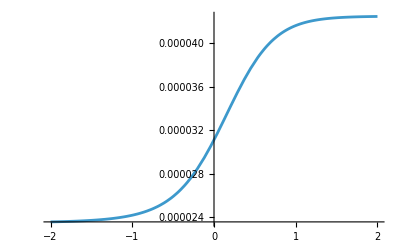

```mathematica
Plot[Im[tInterp2[1.06595,ur]],{ur,-2,2}]
```

t(u), x(u), ṫ(u), ẋ(u) in the complex proper-time plane, plotted with ColorFunction → “CyclicReImLogAbs” (compare Fig. 2 of the paper). Red means real and positive, blue real and negative; black lines are lines of constant real or imaginary part.

The Im = 0 curves of t, x, ṫ, ẋ are overlaid in the last plot: the contour turns horizontal where they intersect.

```mathematica
GraphicsRow[{t,x,tprime,xprime},ImageSize->1300]
```

-Graphics-

## figure 3

```mathematica
Rc=1.06595;
uContour[r_]:=Piecewise[{{r+I Rc,-6<=r<=-Rc},{r-I r,-Rc<=r<=Rc},{r-I Rc,Rc<=r<=6}}];

rVals=Range[-6,6,0.01];

fig3Data=Table[{r,Re[tInterp2[Im[uContour[r]],Re[uContour[r]]]],Im[tInterp2[Im[uContour[r]],Re[uContour[r]]]],Re[xInterp2[Im[uContour[r]],Re[uContour[r]]]],Im[xInterp2[Im[uContour[r]],Re[uContour[r]]]],Re[tdotInterp2[Im[uContour[r]],Re[uContour[r]]]],Im[tdotInterp2[Im[uContour[r]],Re[uContour[r]]]],Re[xdotInterp2[Im[uContour[r]],Re[uContour[r]]]],Im[xdotInterp2[Im[uContour[r]],Re[uContour[r]]]]},{r,rVals}];
```

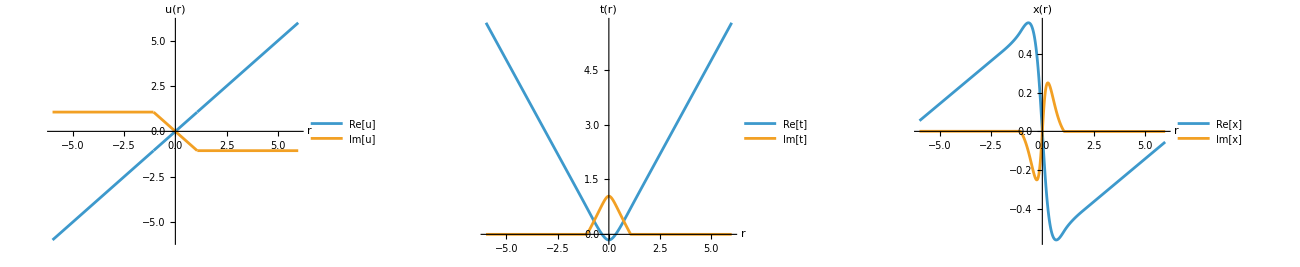

```mathematica
uPlot=Plot[{Re[uContour[r]],Im[uContour[r]]},{r,-6,6},PlotLegends->Placed[{"Re[u]","Im[u]"},{0.8,0.2}],AxesLabel->{"r","u(r)"},AspectRatio->0.6,ImageSize->500];
tPlot=ListLinePlot[{fig3Data[[All,{1,2}]],fig3Data[[All,{1,3}]]},PlotLegends->Placed[{"Re[t]","Im[t]"},{0.8,0.2}],AxesLabel->{"r","t(r)"},AspectRatio->0.6,ImageSize->500];
xPlot=ListLinePlot[{fig3Data[[All,{1,4}]],fig3Data[[All,{1,5}]]},PlotLegends->Placed[{"Re[x]","Im[x]"},{0.8,0.8}],AxesLabel->{"r","x(r)"},AspectRatio->0.6,ImageSize->500];

GraphicsGrid[{{uPlot,tPlot,xPlot}},ImageSize->1300,Spacings->{0.5,0.5}]
tdotPlot=ListLinePlot[{fig3Data[[All,{1,6}]],fig3Data[[All,{1,7}]]},PlotLegends->{"Re[t']","Im[t']"},AxesLabel->{"r","t'(r)"},AspectRatio->0.6,ImageSize->500];
xdotPlot=ListLinePlot[{fig3Data[[All,{1,8}]],fig3Data[[All,{1,9}]]},PlotLegends->{"Re[x']","Im[x']"},AxesLabel->{"r","x'(r)"},AspectRatio->0.6,ImageSize->500];
GraphicsGrid[{{tdotPlot,xdotPlot}},ImageSize->1300,Spacings->{0.5,0.5}]
```

```mathematica
0.57*Exp[-2]
```

0.0771411

```mathematica
Re[xdotInterp2[-Rc,2]]
```

0.0881837

```mathematica
Re[p Exp[-2 A[tInterp2[-Rc,2]]]]
```

0.0881859